# QMC Lookup Table Analysis

This Mathematica notebook is a re-writing of the old Mathematica notebook that analyzes our data to fit the temperature.

THIS IS CF INTERPRATION OF THE RAW CODE, SO IT IS PRONE TO MISTAKES NEED TO CONSULT VV TO CONFIRM MY UNDERSTANDING OF THE CODE

Import packages to make legacy code work with newer version of mathematica (could update function calls but im lazy)

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["NumericalCalculus`"]
Needs["ErrorBarPlots`"]
```

## Introduction

## Fundamental Constants

## Settings and Helper Functions

```mathematica
co={RGBColor[0,0.4470,0.7410],
RGBColor[0.8500, 0.3250, 0.0980],
RGBColor[0.9290, 0.6940, 0.1250],
RGBColor[0.4940, 0.1840, 0.5560],
RGBColor[0.4660, 0.6740, 0.1880],
RGBColor[0.3010, 0.7450, 0.9330],
RGBColor[0.6350, 0.0780, 0.1840]};
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
```

## Trap Parameters

This portion of the code describes the physical parameters of the experiment.  This include the lattice depths and geometries, ODT depths and geometries, and magnetic field.

First define some physical constants of the experiment and display an image of the setup.

```mathematica
λlat=1054 10^-9;(* Lattice wavelength*)
dpx = 0.18 10^-6; (* Distance per pixel of the imaging system (?) *)

Show[Import[FileNameJoin[{NotebookDirectory[],"experiment_geometry.png"}]],ImageSize-> 300]
```

-Graphics-

From this we calculate the angles of the lattice and ODT and define them as unit vectors

```mathematica
θxdt1=57.15/180 π;θxdt2=29.24/180 π;θxlat=30.17/180 π;θylat=31.54/180 π;
vecxdt1=({{Cos[θxdt1]}, {-Sin[θxdt1]}});vecxlat=({{Sin[θxlat]}, {Cos[θxlat]}});vecylat=({{Cos[θylat]}, {-Sin[θylat]}});
```

### Lattice

This portion of the code defines the lattice parameters.

```mathematica
Vlatx=2.5;(* X Lattice depth in Er *)
Vlaty=Vlatx; (* Y Lattice depth in Er *)
Vlatz=Vlatx; (* Z Lattice depth in Er *)
bandnumber=6; (*?*)
```

And then calculate the angle of the lattice?

```mathematica
solangle=Solve[hh+kk*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])==Cos[θxdt1]*Sin[θxlat]-Sin[θxdt1]Cos[θxlat]&&
hh*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])+kk==Cos[θxdt1]*Cos[θylat]+Sin[θxdt1]Sin[θylat],{hh,kk}]
xdt1toxlat=solangle⟦1,1,2⟧;
xdt1toylat=solangle⟦1,2,2⟧;

(*do not project along one lattice direction.Assumption:isotropic cubic lattice (WHAT IS THIS FOR?)*)
xdt1toxlat=1;
xdt1toylat=0;
```

{{hh→-0.432367,kk→0.89142}}

## Density Fitting

To perform the density fit, we analyze a radially averaged data sample at a specific lattice depth, external trap frequency, and magnetic field.

### Input Data

The input data is a text file of TSV data (tab separated values).  The first column is position (in pixels?), the second is the number of atoms, and the third is the error. I assume that the error comes from the radial averaging.

```mathematica
fdataname="2.5Er_206G/temp.txt";(*File location relative to notebook of the TSV data (tab separated values), (position,counts, error)*)

fdataname=FileNameJoin[{NotebookDirectory[],fdataname}];
startid=1; (* 12; Start index to sample data (to avoid issues at the origin for radial data*)
aLMax=100; (* 60; Maximum lattice site to fit*)
```

Load the data in and convert it into lattice sites.

```mathematica
rawdatatemp=ToExpression[Import[fdataname,"TSV"]]; (* Read in data file *)
datainput1=Table[{rawdatatemp⟦ii,1⟧dpx/(λlat/2),rawdatatemp⟦ii,2⟧,rawdatatemp⟦ii,3⟧},{ii,startid,Length[rawdatatemp]}]; (* Convert pixel position to lattice sites *)
datainput=Select[datainput1,#⟦1⟧≤ aLMax&];
```

Plot the initial data.

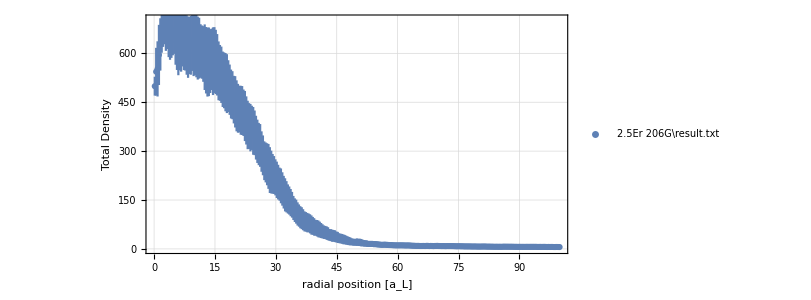

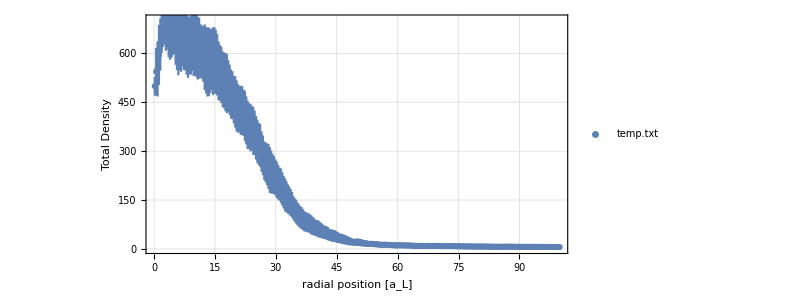

```mathematica
ErrorListPlot[datainput,GridLines->Automatic,ImageSize->600,Frame->True,FrameLabel->{"radial position [a_L]","Total Density"},LabelStyle->Directive[16,Bold,Black],AspectRatio->.5,PlotLegends->Placed[LineLegend[{fname},LabelStyle->18],{Right,Top}]]
```

### Import Fit Data Table

The fit comes from using lookup tables outputted by the QUEST QMC analysis that is done ahead of time. The results of the QMC calculation for varying temperature is stored in a text file. 

The fit output is report as (Nx6) data matrix. It is organized as (temperature (β),singlon density, singlon density error,double density, dublon density error)

Due to issues with brightness calibration, we let the absolute density scale freely.

Import the data.

```mathematica
ffitname="2.5Er_206G/results.txt";
fitdata=ToExpression[Import[ffitname,"TSV"]];
```

Display a list of all temperatures that are included in the calculations (in units of β).

```mathematica
tempβlist=Union[fitdata⟦All,1⟧]
tempβnum=Length[tempβlist];
```

{1.01833,1.0627,1.11111,1.16414,1.22249,1.287,1.3587,1.43885,1.52905,1.63132,1.74825,1.88324,2.04082,2.22717,2.45098,2.7248,3.06748,3.50877,4.09836,4.92611,6.17284,8.26446}

### Do the Fit

To perform the fit, we interpolate the density calculation from the QMC and optimize the least squares error of the interpolation.

```mathematica
fitls={{0}};

For[iitempβ=1,iitempβ≤tempβnum,iitempβ++,
{
tempβcheck=tempβlist⟦iitempβ⟧;
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;

densitycheckfunc=Interpolation[Tβlist⟦All,{2,3}⟧];
densityerrcheckfunc=Interpolation[Tβlist⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist⟦All,{2,6}⟧];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx;
finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*√(densityerrcheckfunc[μfitxx-potential[positionxx,f0]]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0]]^2);

sol=NonlinearModelFit[datainput⟦All,{1,2}⟧,{finalρfunc[xx,μx,ampx,offsetx],1000≤ ampx≤ 2000},{{μx,-1},{ampx,1500},{offsetx,0}},{xx}];
sol1=sol["ParameterTable"];
μfit=sol1⟦1,1,2,2⟧;
ampfit=sol1⟦1,1,3,2⟧;
offsetfit=sol1⟦1,1,4,2⟧;
μfiterr=sol1⟦1,1,2,3⟧;
ampfiterr=sol1⟦1,1,3,3⟧;
offsetfiterr=sol1⟦1,1,4,3⟧;

(*
χlist=Table[(finalρfunc[datainput⟦ii,1⟧,μfit,ampfit,offsetfit]- datainput⟦ii,2⟧ )^2/ampfit^2/(1+0 finalρerrfunc[datainput⟦ii,1⟧,μfit,1 ]^2),{ii,startid,Length[datainput]}];
*)
χlist=Table[(finalρfunc[datainput⟦ii,1⟧,μfit,ampfit,offsetfit]- datainput⟦ii,2⟧ )^2/1/(datainput⟦ii,3⟧^2+finalρerrfunc[datainput⟦ii,1⟧,μfit,1 ]^2),{ii,startid,Length[datainput]}];
χsquare=Total[χlist];

Print[Show[ErrorListPlot[datainput,AxesLabel->{"position(a_L)","density (arb.u.)"}],Plot[finalρfunc[x,μfit,ampfit,offsetfit],{x,0,60}]]];
fitlstemp={{tempβcheck,μfit,ampfit,offsetfit,χsquare,μfiterr,ampfiterr,offsetfiterr}};
Print[fitlstemp];
Print[sol1];
If[ampfit≥ 2500,
{
Print["bad fitting"];
},
fitls=Join[fitls,fitlstemp]
];


}
]
```

NonlinearModelFit::nrnum: The function value 1/2 ((-499.259+1500. (-2 InterpolatingFunction[«5»][«1»]+InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][Plus[«2»]]))^2+(-543.667+1500. (-2 InterpolatingFunction[«5»][«1»]+InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][Plus[«2»]]))^2+«48»+«243») is not a real number at {μx,ampx,offsetx} = {-1.,1500.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {μx,ampx,offsetx} = {-1.,1500.,0.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[«1»] failed at {-1.,1500.,0.}.

NonlinearModelFit::nrnum: The function value 1/2 ((-499.259+1500. (-2 InterpolatingFunction[«5»][«1»]+InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][Plus[«2»]]))^2+(-543.667+1500. (-2 InterpolatingFunction[«5»][«1»]+InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][Plus[«2»]]))^2+«48»+«243») is not a real number at {μx,ampx,offsetx} = {-1.,1500.,0.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {μx,ampx,offsetx} = {-1.,1500.,0.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[«1»] failed at {-1.,1500.,0.}.

NonlinearModelFit::nrnum: The function value 1/2 ((-499.259+1500. (-2 InterpolatingFunction[«5»][«1»]+InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][Plus[«2»]]))^2+(-543.667+1500. (-2 InterpolatingFunction[«5»][«1»]+InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}][Plus[«2»]]))^2+«48»+«243») is not a real number at {μx,ampx,offsetx} = {-1.,1500.,0.}.

$Aborted[]

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

General::stop: Further output of IPOPTMinimize::badobj will be suppressed during this calculation.